```mathematica
listOfSines = Table[{i,Sin[i]},{i,-2Pi,2Pi,.05}];
fun = Interpolation[listOfSines]
max = 30
```

InterpolatingFunction[…]

30

```mathematica
data=RandomVariate[NormalDistribution[0,.5],max]
```

{0.144276,-0.514032,0.679561,0.864646,0.389364,0.394311,0.309287,-0.30679,0.326426,-0.439781,0.281493,-0.323992,0.337134,-0.00877026,0.11185,1.24369,0.613369,0.696056,0.064528,-0.546724,-0.614739,-0.315559,0.433337,0.278867,-0.0683216,-0.0913969,0.583792,0.790658,-1.1816,-0.134599}

```mathematica
listOfRandoms =Table[{-2Pi+i/max*4Pi,data[[i]]},{i,1,max,1}];
data[[2]]
```

-0.514032

```mathematica
playgroundList:=listOfRandoms
```

```mathematica
L[x_,n_]:=LegendreP[n,x]
```

```mathematica
listOfSines[[100]]
```

-0.971903

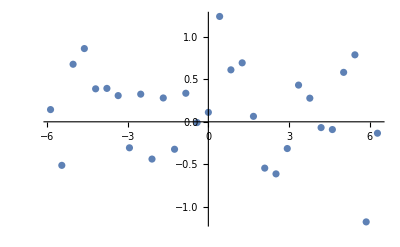

```mathematica
ListPlot@playgroundList
```

```mathematica
quart=Fit[playgroundList,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10},x]
```

0.484596+0.214033 x-0.185965 x^2-0.0514922 x^3+0.00849941 x^4+0.00265883 x^5+0.000909648 x^6-0.0000260891 x^7-0.0000609378 x^8-4.20535×10^-7 x^9+9.10557×10^-7 x^10

4.36632×10^-6 (3-30 x^2+35 x^4)

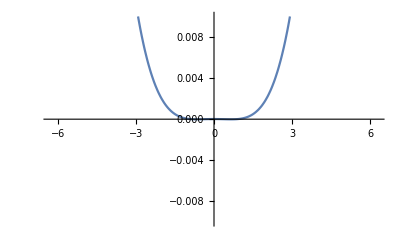

```mathematica
quart2=Fit[playgroundList,{LegendreP[4,x]},x]
Plot[quart2,{x,-2Pi,2Pi},PlotRange->{{-2Pi,2Pi},{-.01,.01}}]
```

```mathematica
fList=Re@FourierSeries[quart,x,5]
```

0.106817+Re[(0.182668+0.0645158 ⅈ) ⅇ^(-ⅈ x)+(0.182668-0.0645158 ⅈ) ⅇ^(ⅈ x)+(0.0140079+0.0400998 ⅈ) ⅇ^(-2 ⅈ x)+(0.0140079-0.0400998 ⅈ) ⅇ^(2 ⅈ x)-(0.0122116+0.0243014 ⅈ) ⅇ^(-3 ⅈ x)-(0.0122116-0.0243014 ⅈ) ⅇ^(3 ⅈ x)+(0.00717051+0.0173115 ⅈ) ⅇ^(-4 ⅈ x)+(0.00717051-0.0173115 ⅈ) ⅇ^(4 ⅈ x)-(0.00459934+0.0134927 ⅈ) ⅇ^(-5 ⅈ x)-(0.00459934-0.0134927 ⅈ) ⅇ^(5 ⅈ x)]

Re[(0.0645158-0.182668 ⅈ) ⅇ^(-ⅈ x)+(0.0645158+0.182668 ⅈ) ⅇ^(ⅈ x)+(0.0801995-0.0280158 ⅈ) ⅇ^(-2 ⅈ x)+(0.0801995+0.0280158 ⅈ) ⅇ^(2 ⅈ x)-(0.0729043-0.0366349 ⅈ) ⅇ^(-3 ⅈ x)-(0.0729043+0.0366349 ⅈ) ⅇ^(3 ⅈ x)+(0.0692461-0.0286821 ⅈ) ⅇ^(-4 ⅈ x)+(0.0692461+0.0286821 ⅈ) ⅇ^(4 ⅈ x)]

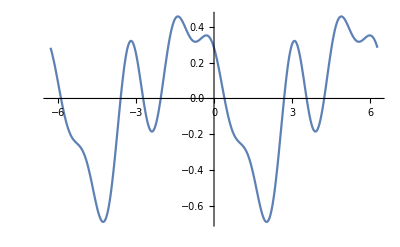

```mathematica
deeFun=Re@D[FourierSeries[quart,x,4],x]
Plot[deeFun,{x,-2Pi,2Pi},PlotRange->All]
```

```mathematica
Function[x,Evaluate[deeFun]]
%[2Pi+.2]
```

Function[x,Re[(0.0645158-0.182668 ⅈ) ⅇ^(-ⅈ x)+(0.0645158+0.182668 ⅈ) ⅇ^(ⅈ x)+(0.0801995-0.0280158 ⅈ) ⅇ^(-2 ⅈ x)+(0.0801995+0.0280158 ⅈ) ⅇ^(2 ⅈ x)-(0.0729043-0.0366349 ⅈ) ⅇ^(-3 ⅈ x)-(0.0729043+0.0366349 ⅈ) ⅇ^(3 ⅈ x)+(0.0692461-0.0286821 ⅈ) ⅇ^(-4 ⅈ x)+(0.0692461+0.0286821 ⅈ) ⅇ^(4 ⅈ x)]]

0.156164

```mathematica
Function[x,Evaluate[deeFun]]

(*%[3]
h=.05
ray[x_]:=(%[x+h]-%[x])/h*)
rayExtra =Table[{2Pi+i/10*.2,(%[2Pi+i/10*.2+.001]-%[2Pi+i/10*.2])/(.001)},{i,1,10,1}]
```

Function[x,Re[(0.0645158-0.182668 ⅈ) ⅇ^(-ⅈ x)+(0.0645158+0.182668 ⅈ) ⅇ^(ⅈ x)+(0.0801995-0.0280158 ⅈ) ⅇ^(-2 ⅈ x)+(0.0801995+0.0280158 ⅈ) ⅇ^(2 ⅈ x)-(0.0729043-0.0366349 ⅈ) ⅇ^(-3 ⅈ x)-(0.0729043+0.0366349 ⅈ) ⅇ^(3 ⅈ x)+(0.0692461-0.0286821 ⅈ) ⅇ^(-4 ⅈ x)+(0.0692461+0.0286821 ⅈ) ⅇ^(4 ⅈ x)]]

{{6.30319,-0.520804},{6.32319,-0.552511},{6.34319,-0.582805},{6.36319,-0.611498},{6.38319,-0.638414},{6.40319,-0.663386},{6.42319,-0.686264},{6.44319,-0.706911},{6.46319,-0.725207},{6.48319,-0.741046}}

{{1,20. (-0[6.30319]+0[6.35319])},{2,20. (-0[6.32319]+0[6.37319])},{3,20. (-0[6.34319]+0[6.39319])},{4,20. (-0[6.36319]+0[6.41319])},{5,20. (-0[6.38319]+0[6.43319])},{6,20. (-0[6.40319]+0[6.45319])},{7,20. (-0[6.42319]+0[6.47319])},{8,20. (-0[6.44319]+0[6.49319])},{9,20. (-0[6.46319]+0[6.51319])},{10,20. (-0[6.48319]+0[6.53319])}}

```mathematica
rayExtra=0
```

0

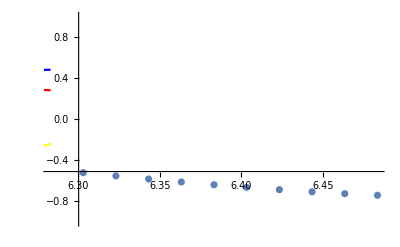

```mathematica
(*Plot[fList,{x,-1,1}]*)
Show[ListPlot@rayExtra,Plot[{quart,deeFun,fList},{x,-2Pi,2Pi},PlotStyle->{Yellow,Red,Blue}],PlotRange->{{2Pi,2Pi+10/10*.2},{-1,1}}]
```

```mathematica
s[n_,x_]=Sin[n*Pi*x/2]
c[n_,x_]=Cos[n*Pi*x/2]
```

Sin[(n π x)/2]

Cos[(n π x)/2]

```mathematica
f[x_]:=Fit[listOfSines,{1,x,x^2,x^3,x^4,x^5},x]
```

```mathematica
(*f[x_]:= Piecewise[{{Abs[x],Abs[x]≤ Pi}}]*)
IP[f_,g_]:=Integrate[f g ,{x,-2,2}]
```

```mathematica
a0[func_]:=IP[func[x],c[0,x]]
aFC[func_,n_]:=IP[func[x],c[n,x]]
bFC[func_,n_]:=IP[func[x],s[n,x]]
```

```mathematica
FSeries[func_,N_,x_]:=a0[func]/2+Sum[aFC[func,n]c[n,x]+bFC[func,n]*s[n,x],{n,1,N}]
```

```mathematica
Simplify[Sin[n*Pi],Element[n,Integers]]
Simplify[Cos[n*Pi],Element[n,Integers]]
Simplify[Sin[(2n-1)*Pi/2],Element[n,Integers]]
Simplify[Sin[(2n-1)*Pi/2],Element[n,Integers]]
```

0

(-1)^n

(-1)^(1+n)

(-1)^(1+n)

```mathematica
fs10[x_]=FSeries[f,50,x]
```

-1.41651+(0.0162774+0. ⅈ) Cos[(π x)/2]-0.00406994 Cos[π x]+0.00180891 Cos[(3 π x)/2]-(0.00101752+0. ⅈ) Cos[2 π x]+0.000651218 Cos[(5 π x)/2]-0.000452236 Cos[3 π x]+(0.000332255+0. ⅈ) Cos[(7 π x)/2]-0.000254383 Cos[4 π x]+(0.000200994+0. ⅈ) Cos[(9 π x)/2]-0.000162805 Cos[5 π x]+(0.00013455+0. ⅈ) Cos[(11 π x)/2]-0.000113059 Cos[6 π x]+0.0000963346 Cos[(13 π x)/2]-(0.000083064+0. ⅈ) Cos[7 π x]+(0.000072358+0. ⅈ) Cos[(15 π x)/2]-0.0000635959 Cos[8 π x]+0.0000563341 Cos[(17 π x)/2]-(0.0000502486+0. ⅈ) Cos[9 π x]+0.0000450985 Cos[(19 π x)/2]-0.0000407014 Cos[10 π x]+0.0000369174 Cos[(21 π x)/2]-0.0000336375 Cos[11 π x]+(0.0000307761+0. ⅈ) Cos[(23 π x)/2]-(0.0000282649+0. ⅈ) Cos[12 π x]+0.0000260489 Cos[(25 π x)/2]-0.0000240837 Cos[13 π x]+0.0000223327 Cos[(27 π x)/2]-0.000020766 Cos[14 π x]+0.0000193586 Cos[(29 π x)/2]-(0.0000180895+0. ⅈ) Cos[15 π x]+0.0000169413 Cos[(31 π x)/2]-(0.000015899+0. ⅈ) Cos[16 π x]+(0.00001495+0. ⅈ) Cos[(33 π x)/2]-0.0000140835 Cos[17 π x]+0.0000132903 Cos[(35 π x)/2]-(0.0000125622+0. ⅈ) Cos[18 π x]+0.0000118923 Cos[(37 π x)/2]-0.0000112746 Cos[19 π x]+0.0000107039 Cos[(39 π x)/2]-(0.0000101754+0. ⅈ) Cos[20 π x]+9.68505×10^-6 Cos[(41 π x)/2]-(9.22935×10^-6+0. ⅈ) Cos[21 π x]+8.80507×10^-6 Cos[(43 π x)/2]-(8.40938×10^-6+0. ⅈ) Cos[22 π x]+8.03979×10^-6 Cos[(45 π x)/2]-7.69403×10^-6 Cos[23 π x]+7.37011×10^-6 Cos[(47 π x)/2]-(7.06622×10^-6+0. ⅈ) Cos[24 π x]+6.78074×10^-6 Cos[(49 π x)/2]-6.51223×10^-6 Cos[25 π x]+(0.43416-1.02707×10^-18 ⅈ) Sin[(π x)/2]-0.217197 Sin[π x]+0.144813 Sin[(3 π x)/2]-(0.108613-4.67491×10^-19 ⅈ) Sin[2 π x]+0.0868921 Sin[(5 π x)/2]-0.0724108 Sin[3 π x]+0.0620667 Sin[(7 π x)/2]-(0.0543085+0. ⅈ) Sin[4 π x]+(0.0482744+1.52958×10^-32 ⅈ) Sin[(9 π x)/2]-(0.043447+0. ⅈ) Sin[5 π x]+(0.0394973-6.79987×10^-32 ⅈ) Sin[(11 π x)/2]-(0.0362059+0. ⅈ) Sin[6 π x]+(0.0334209+0. ⅈ) Sin[(13 π x)/2]-0.0310337 Sin[7 π x]+0.0289648 Sin[(15 π x)/2]-0.0271545 Sin[8 π x]+(0.0255572+0. ⅈ) Sin[(17 π x)/2]-0.0241374 Sin[9 π x]+0.022867 Sin[(19 π x)/2]-(0.0217236+0. ⅈ) Sin[10 π x]+0.0206892 Sin[(21 π x)/2]-0.0197488 Sin[11 π x]+0.0188901 Sin[(23 π x)/2]-(0.018103-3.28396×10^-21 ⅈ) Sin[12 π x]+0.0173789 Sin[(25 π x)/2]-0.0167105 Sin[13 π x]+(0.0160916+0. ⅈ) Sin[(27 π x)/2]-0.0155169 Sin[14 π x]+0.0149818 Sin[(29 π x)/2]-(0.0144824-3.73984×10^-32 ⅈ) Sin[15 π x]+0.0140153 Sin[(31 π x)/2]-(0.0135773-1.33075×10^-21 ⅈ) Sin[16 π x]+(0.0131658+5.36473×10^-22 ⅈ) Sin[(33 π x)/2]-0.0127786 Sin[17 π x]+0.0124135 Sin[(35 π x)/2]-(0.0120687-2.04137×10^-22 ⅈ) Sin[18 π x]+0.0117425 Sin[(37 π x)/2]-0.0114335 Sin[19 π x]+0.0111403 Sin[(39 π x)/2]-0.0108618 Sin[20 π x]+(0.0105969+0. ⅈ) Sin[(41 π x)/2]-(0.0103446+6.80675×10^-33 ⅈ) Sin[21 π x]+(0.010104+0. ⅈ) Sin[(43 π x)/2]-0.00987439 Sin[22 π x]+0.00965496 Sin[(45 π x)/2]-0.00944507 Sin[23 π x]+0.00924411 Sin[(47 π x)/2]-(0.00905152-2.20992×10^-21 ⅈ) Sin[24 π x]+0.0088668 Sin[(49 π x)/2]-0.00868946 Sin[25 π x]

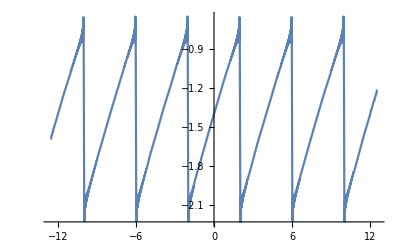

```mathematica
Plot[fs10[x],{x,-4Pi,4Pi},PlotRange->All	]
```